LHC Data Exploration using Wolfram Language

Kovalchuk Nataliia

Salvarezza Matteo

University of Hamburg

Most representative image

-Graphics--Graphics--Graphics-

Abstract

GOAL OF THE PROJECT: to write the functionality that extract and analyze the experimental data recorded by the CMS experiment during proton-proton (pp) collision at the Large Hadron Collider (LHC).

SUMMARY OF WORK: first steps in the analyzing the LHC data in Mathematica are performed in this work. The data extraction was done in two steps: 1) using CMS open software to select the sample from the  primary datasets; 2) using Mathematica to  import the  data from reduced root files and text files. The collision events visualization functionality was carried out in this work as well as the functionalities for kinematic variables calculation were written. The basic event selection was implemented, applying the cuts on the variables relevant in the analysis.

RESULTS AND FUTURE  WORK: the functionality was successfully implemented and the data was submitted to data repository. A better transition between Mathematica and CMS software need to be implemented in order to access the primary data easily and faster. Simulated Monte Carlo data should be used together with the real data, in order to control the signal and background events. The syntax for the events selection in Mathematica need to be simplified.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

How to get started analyzing the data from the Large Hadron Collider (LHC)?

The source to the LHC data:
- go to the CERN Open Data Portal: http://opendata.cern.ch
- choose the experiment the data you want to analyse the most (in this note the data from the CMS experiment will be processed )

Data format:
The data taking at the LHC are performed during the several runs, where each run may have a several proton-proton (pp) collisions, events. The original data for each physical run is stored in the ROOT format and are available on http://opendata.cern.ch/research/CMS.

In current work the Single Muon primary data, recorded during RunA period in 2011 with collision energy 7 TeV, are used:
0C0E1024-C13D-E311-BD49-003048F1C762.root .
(DOI: 10.7483/OPENDATA.CMS.UY8U.9XJ3)

Having in mind that the primary datasets are very large and have a complicated structure, one may want to extract only necessary information for his/her study before analysing it in Mathematica.

To do this follow the instruction from http://opendata.cern.ch/VM/CMS#2011:

- setup the CMS Virtual Machine:

download the VirtualBox and use next commands in terminal
cmsrel CMSSW_5_3_32
cd CMSSW_5_3_32/src/
cmsenv

- get the package for the basic data analysing: https://twiki.cern.ch/twiki/bin/view/CMSPublic/WorkBookFWLiteExamples

git cms-addpkg PhysicsTools/FWLite

- download https://github.com/kovalch/WSS/blob/master/FWLiteHistograms.cc
to CMSSW_5_3_32/src/PhysicsTools/FWLite/bin/.

- compile and run the script 
cd CMSSW_5_3_32/src/
scram b 
FWLiteHistograms inputFiles=0C0E1024-C13D-E311-BD49-003048F1C762.root outputFile=analyzeFWLite.root

where as inputFiles one may use different root files chosen for the analysis.

The output files: analyzeFWLite.root and file.txt can be used in Mathematica.


To read the output root files in Mathematica importer package should be used as explained at https://arxiv.org/pdf/1102.5068.pdf
All needed source are available here: http://library.wolfram.com/infocenter/Articles/7793/


Now you are ready to analyse the LHC data!

Code and Visualizations

all details on the GitHub

How to import the data from file.txt  file and to analyze the data:

```mathematica
import = Import["/Users/mac/Downloads/MyF/file.txt", "Text"];
```

```mathematica
removenumbers = StringReplace[import, a:DigitCharacter.. ~~ "." ~~ b:DigitCharacter..~~"e"~~s:RepeatedNull["-"|"+"]~~ c:DigitCharacter.. :>ToString[AccountingForm[N[ToExpression@StringJoin[a <>"."<>b<>"^"<>s<>c]], NumberSigns -> {"-", ""}]]];
```

```mathematica
expression=ToExpression@removenumbers;
```

```mathematica
data=Map[Evaluate,expression/.Null->Nothing, Infinity];
```

Data control

```mathematica
Length@data
```

1226

```mathematica
ByteCount@dataset
```

162058352

```mathematica
dataset=Dataset@data
```

Dataset[<>]

```mathematica
Rasterize[dataset]
```

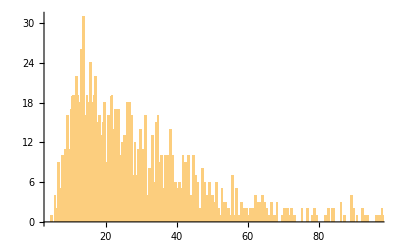

```mathematica
Histogram[Normal@datasetFull[[All,"Particles","Jets",1,"TransverseMomentum"]],{0.5}]
```

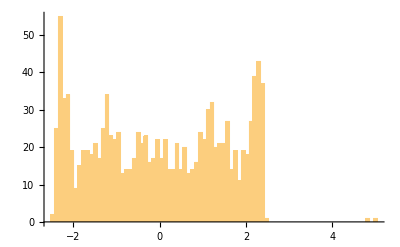

```mathematica
Histogram[Normal@datasetFull[[All,"Particles","Muons",1,"Pseudorapidity"]],{0.09}]
```

```mathematica
particle1=dataset[[1,1,3,3]]
```

Dataset[<>]

```mathematica
particle2=dataset[[1,1,3,4]]
```

Dataset[<>]

### Kinematic Variables Formulas

```mathematica
energyFormula[particle_] := Sqrt[(particle["TransverseMomentum"]*Cosh[particle["Pseudorapidity"]])^2 + particle["Mass"]^2]
```

```mathematica
pXFormula[particle_]:= particle["TransverseMomentum"] * Cos[particle["AzimuthalAngle"]]
```

```mathematica
pYFormula[particle_] :=  particle["TransverseMomentum"] * Sin[particle["AzimuthalAngle"]]
```

```mathematica
pZFormula[particle_] := particle["TransverseMomentum"] * Sinh[particle["Pseudorapidity"]]
```

Particle three-momentum:

```mathematica
threeMomentumFormula [particle_]:= {pXFormula[particle], pYFormula[particle], pZFormula[particle]}
```

Particle four-momentum:

```mathematica
fourMomentumFormula[particle_]:={energyFormula[particle],pXFormula[particle], pYFormula[particle], pZFormula[particle]}
```

Polar angle, the angle between the particle three-momentum and the positive direction of the beam axis:

```mathematica
polarAngleFormula[particle_] := 2*ArcTan[Exp[-1*particle["Pseudorapidity"]]]
```

Angular separation between particles:

```mathematica
deltaRFormula[particle1_,particle2_] := Sqrt[(particle1["Pseudorapidity"] - particle2["Pseudorapidity"])^2+(particle1["AzimuthalAngle"] - particle2["AzimuthalAngle"])^2]
```

### Kinematic Variables

```mathematica
energy[eventNumber_,objectName_,particleName_ , particleNumber_] := Flatten@Normal[dataset[[eventNumber,objectName, particleName, particleNumber]]] /. a_Association :>energyFormula[a]
```

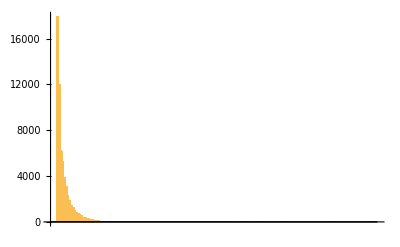
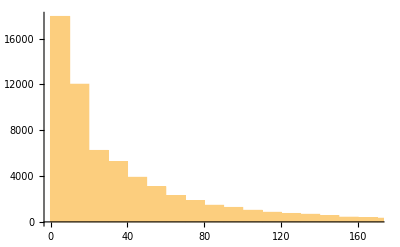

```mathematica
{BarChart[Last[HistogramList[energy[All,"Particles","Jets",All]]]],Histogram[energy[All,"Particles","Jets",All]]}
```

```mathematica
pX[eventNumber_,objectName_,particleName_ , particleNumber_] := Flatten@Normal[dataset[[eventNumber,objectName, particleName, particleNumber]]] /. a_Association :>pXFormula[a]
```

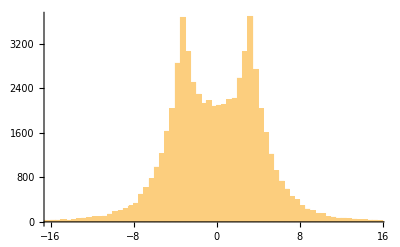

```mathematica
Histogram[pX[All,"Particles","Jets",All],{0.5}]
```

```mathematica
pY[eventNumber_,objectName_,particleName_ , particleNumber_] := Flatten@Normal[dataset[[eventNumber,objectName, particleName, particleNumber]]] /. a_Association :>pYFormula[a]
```

```mathematica
pZ[eventNumber_,objectName_,particleName_ , particleNumber_] := Flatten@Normal[dataset[[eventNumber,objectName, particleName, particleNumber]]] /. a_Association :>pZFormula[a]
```

```mathematica
threeMomentum[eventNumber_,objectName_,particleName_ , particleNumber_] := ReleaseHold[Flatten@Normal[dataset[[eventNumber,objectName, particleName, particleNumber]]] /. a_Association :>Hold[threeMomentumFormula[a]]]
```

```mathematica
fourMomentum[eventNumber_,objectName_,particleName_ , particleNumber_] := ReleaseHold[Flatten@Normal[dataset[[eventNumber,objectName, particleName, particleNumber]]] /. a_Association :>Hold[fourMomentumFormula[a]]]
```

```mathematica
polarAngle[eventNumber_,objectName_,particleName_ , particleNumber_] := Flatten@Normal[dataset[[eventNumber,objectName, particleName, particleNumber]]] /. a_Association :>polarAngleFormula[a]
```

```mathematica
deltaR[eventNumber_,objectName1_,particleName1_ , particleNumber1_,objectName2_,particleName2_ , particleNumber2_] := deltaRFormula[dataset[[eventNumber,objectName1, particleNumber1, particleNumber1]],dataset[[eventNumber,objectName2, particleName2,particleNumber2]]]
```

```mathematica
deltaR[1,"Particles","Jets",1,"Particles","Jets",2]
```

0.0296654

```mathematica
numberOfParticles[eventNumber_,objectName_,particleName_] := Length[dataset[[eventNumber,objectName,particleName]]]
```

### Basic selection

```mathematica
applyCut[object_,type_,filter_,n_ ,operator_][event_]:=operator[Length[Select[event[[object,type]],filter]],n]
```

Select an event with exactly one muon which has transverse momentum greater than 20 GeV and pseudorapidity less than 2,1.

```mathematica
datasetOneMuon = dataset[Select[applyCut["Particles","Muons",True&,1,Equal]]]
```

```mathematica
datasetMuonCuts = datasetOneMuon[Select[applyCut["Particles","Muons",#TransverseMomentum>20 && Abs[#Pseudorapidity]<2.1&,1,Equal]]]
```

Dataset[<>]

Out of remaining events  to select the events that have not more than 10 jets

```mathematica
datasetSixJets = datasetMuonCuts[Select[applyCut["Particles","Jets",True&,10,Less]]]
```

Dataset[<>]

### Events visualization for the selected events

```mathematica
nEv=2;
datasetSixJets[[nEv,"Particles"]]
dataset=datasetSixJets;
momMuons=threeMomentum[nEv,"Particles","Muons",All];
momJets=threeMomentum[nEv,"Particles","Jets",All];
momElectrons=threeMomentum[nEv,"Particles","Electrons",All];
momPhotons=threeMomentum[nEv,"Particles","Photons",All];
```

Dataset[<>]

```mathematica
Graphics3D[{Style[Line[{{0,0,0},Normalize[#]}],Hue[.99],Thickness[Log@Norm[#]/200]]&/@momMuons, Style[Line[{{0,0,0},Normalize[#]}],Hue[.6],Thickness[Log@Norm[#]/300]]&/@momJets,
Style[Line[{{0,0,0},Normalize[#]}],Hue[.43],Thickness[Log@Norm[#]/200]]&/@momElectrons,
Style[Line[{{0,0,0},Normalize[#]}],Thickness[Log@Norm[#]/200]]&/@momPhotons}, Axes -> True, AxesLabel->{x, y, z}]
```

-Graphics3D-

### Events visualization for the all events

```mathematica
nEv=140
dataset=datasetFull;
momMuons=threeMomentum[nEv,"Particles","Muons",All];
momJets=threeMomentum[nEv,"Particles","Jets",All];
momElectrons=threeMomentum[nEv,"Particles","Electrons",All];
momPhotons=threeMomentum[nEv,"Particles","Photons",All];
```

140

```mathematica
nEv
paricleInfo= dataset[nEv,"Particles","Muons"]
```

6

Dataset[<>]

```mathematica
Legended
```

```mathematica
Legended[Graphics3D[{Style[Line[{{0,0,0},Normalize[#]}],Hue[.99],Thickness[Log@Norm[#]/200]]&/@momMuons, Style[Line[{{0,0,0},Normalize[#]}],Hue[.6],Thickness[Log@Norm[#]/300]]&/@momJets,
Style[Line[{{0,0,0},Normalize[#]}],Hue[.43],Thickness[Log@Norm[#]/200]]&/@momElectrons,
Style[Line[{{0,0,0},Normalize[#]}],Thickness[Log@Norm[#]/200]]&/@momPhotons}, Axes -> True, AxesLabel->{x, y, z} ],LineLegend[{Red,Blue,Green, Black},{"Muon","Jets","Electron", "Photon"}]]
```

```mathematica
Table[Graphics3D[{
Style[Line[{{0,0,0},Normalize[#]}],Hue[.99],Thickness[0.02]]&/@threeMomentum[i,"Particles","Muons",All],ViewPoint->{-3,-1.75,0},
Style[Line[{{0,0,0},Normalize[#]}],Hue[.6],Thickness[Log@Norm[#]/200]]&/@threeMomentum[i,"Particles","Jets",All],ViewPoint->{-3,-1.75,0},
Style[Line[{{0,0,0},Normalize[#]}],Hue[.43],Thickness[0.02]]&/@threeMomentum[i,"Particles","Electrons",All],ViewPoint->{-3,-1.75,0},
Style[Line[{{0,0,0},Normalize[#]}],Thickness[0.02]]&/@threeMomentum[i,"Particles","Photons",All],ViewPoint->{-3,-1.75,0} }]
,{i,100,110}
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
FeatureSpacePlot[%]
```

-Graphics-

```mathematica
Table[Graphics3D[{
Style[Line[{{0,0,0},Normalize[#]}],Hue[.99],Thickness[0.02]]&/@threeMomentum[i,"Particles","Muons",All],ViewPoint->{-3,-1.75,0},
Style[Line[{{0,0,0},Normalize[#]}],Hue[.6],Thickness[Log@Norm[#]/200]]&/@threeMomentum[i,"Particles","Jets",All],ViewPoint->{-3,-1.75,0},
Style[Line[{{0,0,0},Normalize[#]}],Hue[.43],Thickness[0.02]]&/@threeMomentum[i,"Particles","Electrons",All],ViewPoint->{-3,-1.75,0},
Style[Line[{{0,0,0},Normalize[#]}],Thickness[0.02]]&/@threeMomentum[i,"Particles","Photons",All],ViewPoint->{-3,-1.75,0} }]
,{i,1,120}
];
```

```mathematica
FeatureSpacePlot[%]
```

-Graphics-

How to import the data from analyzeFWLite.root  file.

To show which variables are stored in the root file.

```mathematica
Import["/Users/mac/Downloads/MyF/analyzeFWLite.root","ROOT"]
```

{{muonPx,px,TH1F},{muonPy,py,TH1F},{muonEt,et,TH1F},{muonPt,pt,TH1F},{muonEta,eta,TH1F},{muonPhi,phi,TH1F},{mumuMass,mass,TH1F},{electronPt,pt,TH1F},{electronEta,eta,TH1F},{electronPhi,phi,TH1F},{jetPt,pt,TH1F},{jetEta,eta,TH1F},{jetPhi,phi,TH1F},{metPt,pt,TH1F},{metEta,eta,TH1F},{metPhi,phi,TH1F},{photonPt,pt,TH1F},{photonEta,eta,TH1F},{photonPhi,phi,TH1F}}

To see the format of the information written to the histograms in root file:

```mathematica
muonPy =Import["/Users/mac/Downloads/MyF/analyzeFWLite.root",{"ROOT","TH1FData","muonPy"}]
```

{{0.,3.,669.,25.865},{3.,3.,161.,12.6886},{6.,3.,51.,7.14143},{9.,3.,55.,7.4162},{12.,3.,30.,5.47723},{15.,3.,43.,6.55744},{18.,3.,34.,5.83095},{21.,3.,22.,4.69042},{24.,3.,24.,4.89898},{27.,3.,24.,4.89898},{30.,3.,15.,3.87298},{33.,3.,13.,3.60555},{36.,3.,11.,3.31662},{39.,3.,2.,1.41421},{42.,3.,6.,2.44949},{45.,3.,7.,2.64575},{48.,3.,1.,1.},{51.,3.,1.,1.},{54.,3.,0.,0.},{57.,3.,1.,1.},{60.,3.,1.,1.},{63.,3.,1.,1.},{66.,3.,1.,1.},{69.,3.,0.,0.},{72.,3.,0.,0.},{75.,3.,0.,0.},{78.,3.,0.,0.},{81.,3.,1.,1.},{84.,3.,0.,0.},{87.,3.,2.,1.41421},{90.,3.,0.,0.},{93.,3.,0.,0.},{96.,3.,0.,0.},{99.,3.,0.,0.},{102.,3.,0.,0.},{105.,3.,0.,0.},{108.,3.,0.,0.},{111.,3.,0.,0.},{114.,3.,0.,0.},{117.,3.,0.,0.},{120.,3.,0.,0.},{123.,3.,0.,0.},{126.,3.,0.,0.},{129.,3.,0.,0.},{132.,3.,0.,0.},{135.,3.,0.,0.},{138.,3.,0.,0.},{141.,3.,0.,0.},{144.,3.,0.,0.},{147.,3.,0.,0.},{150.,3.,0.,0.},{153.,3.,0.,0.},{156.,3.,0.,0.},{159.,3.,0.,0.},{162.,3.,0.,0.},{165.,3.,0.,0.},{168.,3.,0.,0.},{171.,3.,0.,0.},{174.,3.,0.,0.},{177.,3.,0.,0.},{180.,3.,0.,0.},{183.,3.,0.,0.},{186.,3.,0.,0.},{189.,3.,0.,0.},{192.,3.,0.,0.},{195.,3.,0.,0.},{198.,3.,0.,0.},{201.,3.,0.,0.},{204.,3.,0.,0.},{207.,3.,0.,0.},{210.,3.,0.,0.},{213.,3.,0.,0.},{216.,3.,0.,0.},{219.,3.,0.,0.},{222.,3.,0.,0.},{225.,3.,0.,0.},{228.,3.,0.,0.},{231.,3.,0.,0.},{234.,3.,0.,0.},{237.,3.,0.,0.},{240.,3.,0.,0.},{243.,3.,0.,0.},{246.,3.,0.,0.},{249.,3.,0.,0.},{252.,3.,0.,0.},{255.,3.,0.,0.},{258.,3.,0.,0.},{261.,3.,0.,0.},{264.,3.,0.,0.},{267.,3.,0.,0.},{270.,3.,0.,0.},{273.,3.,0.,0.},{276.,3.,0.,0.},{279.,3.,0.,0.},{282.,3.,0.,0.},{285.,3.,0.,0.},{288.,3.,0.,0.},{291.,3.,0.,0.},{294.,3.,0.,0.},{297.,3.,0.,0.}}

The data form:   { {x1, Δx1, count1, error1}, {x2, Δx2, count2, error2}, ... }

```mathematica
head={"x","Δx","count","Δcount"};
Grid[Join[{head},Take[muonPy,10]],Frame-> All]
```

x | Δx | count | Δcount
0. | 3. | 669. | 25.865
3. | 3. | 161. | 12.6886
6. | 3. | 51. | 7.14143
9. | 3. | 55. | 7.4162
12. | 3. | 30. | 5.47723
15. | 3. | 43. | 6.55744
18. | 3. | 34. | 5.83095
21. | 3. | 22. | 4.69042
24. | 3. | 24. | 4.89898
27. | 3. | 24. | 4.89898

To plot:

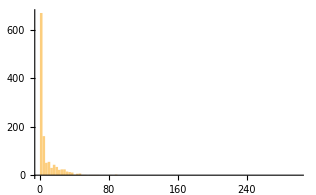

```mathematica
graphics1MuonPy=Import["/Users/mac/Downloads/MyF/analyzeFWLite.root",{"ROOT","TH1FGraphics","muonPy"}]
```

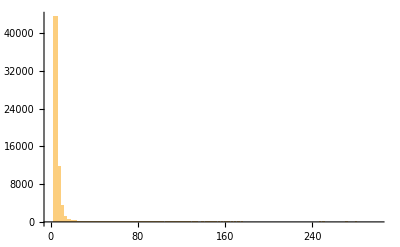

```mathematica
graphics1JetPt=Import["/Users/mac/Downloads/MyF/analyzeFWLite.root",{"ROOT","TH1FGraphics","jetPt"}]
```

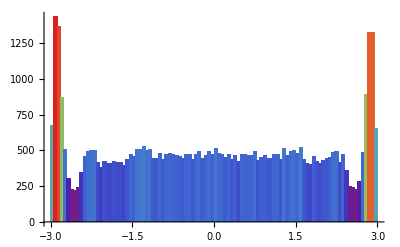

```mathematica
graphics2JetEta=Import["/Users/mac/Downloads/MyF/analyzeFWLite.root",{"ROOT","TH1FGraphics","jetEta"},ColorFunction->Function[{height},ColorData["Rainbow"][height]]]
```

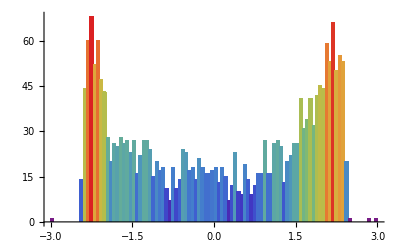

```mathematica
graphics2MuonEta=Import["/Users/mac/Downloads/MyF/analyzeFWLite.root",{"ROOT","TH1FGraphics","muonEta"},ColorFunction->Function[{height},ColorData["Rainbow"][height]]]
```

Link to the GitHub

Explicit code

Written Content / Lesson Plans

Conclusions in Detail

The first test on the analysing the LHC data was done. The better transition between Mathematica and CMS software need to be implemented in order to access the data easily and faster. The way to select events in mathematica is still quite complicated.

All Visualizations

Data Sources Links/References

Analyzed data is available at Data Resource repository:

Future Directions

Background Info Links/References

Keywords

dataanalysis

LHC

CMS

HEP

ROOT

Other

Date

Last Modified: Monday, July 03, 2017

```mathematica
"Add Timestamp"
```